```mathematica
makeChain[n_] := Table[0, {i, n}]
makeEmptyIndexes[n_] :=  Table[i, {i,1, n}]
createNeighbours[node_] := {node - 1, node + 1}
inBoundaries[node_, N_] := node >= 1 && node ≤ N
```

```mathematica
findIsolatedClusters[chain_, startNode_, chainSize_] := {(* initialization *) isolatedClusterCount = 0; isolatedCount = 0;
howLong = Length[chain];
startNodes =Join[{startNode}, Select[createNeighbours[startNode], # ≥ 1 && # ≤ chainSize &]]; 
visited={};
 toVisit = {};centers = {};
While[Length[startNodes] > 0 ,firstNode = Extract[startNodes,1]; startNodes = startNodes[[2;;]];
toVisit = Append[toVisit, firstNode];
currentType = chain[[firstNode]];
currentCount = 0; (* used to count how many members are in cluster if it's a cluster *)
fine = False;
While[Length[toVisit] > 0, node = Extract[toVisit, 1]; toVisit = toVisit[[2;;]];
nodeType = chain[[node]];
If[nodeType == 0,fine = True;, If[nodeType == currentType,
currentCount ++;visited = Append[visited, node]; startNodes = DeleteCases[startNodes, node]; neighbours = createNeighbours[node];
toVisit = Join[toVisit, Select[neighbours, inBoundaries[#, howLong] && !MemberQ[visited, #] &]];
If[Length[Select[neighbours, !inBoundaries[#, howLong]&]] > 0, fine=True];];];
];If[!fine, (* we found an isolated cluster *) isolatedClusterCount++; centers = Append[centers, firstNode]; isolatedCount = isolatedCount + currentCount;]];
{isolatedClusterCount, centers, isolatedCount}}
```

```mathematica
getFromRandomChoice[arg_] := RandomChoice[Table[i, {i, 1, arg}]];
```

```mathematica
simulateChain[maxLength_, typeGenerator_: getFromRandomChoice, arg_:2] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexes[maxLen];
chain = makeChain[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
chain[[x]] = typeGenerator[arg]; 

clusters = findIsolatedClusters[chain, x, maxLength];
isolated = clusters[[1, 3]];

allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

```mathematica
Timing[maxLen = 1000;
countsArrayAll ={};
countsArray = simulateChain[maxLen];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
```

{0.1693,Null}

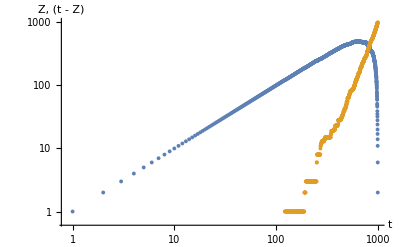

```mathematica
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
maxLen = 1000;

For[i=0,i<20,i++,countsArray = simulateChain[maxLen, 2];Z = countsArray[[2]];
Clear[x];
qp = ListPlot[Z];
fit = Fit[Z, { 1 ,x, x^2,  x^3}, x ];
]
```

10.7022 x^(2/3)

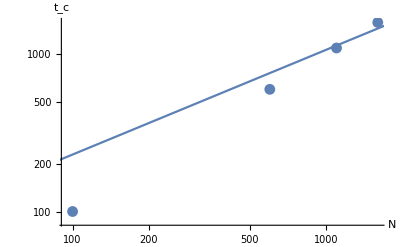

```mathematica
allTCs = {};
allMeanTCs = {};
maxLens = {};
For[g= 100, g < 2000,g+= 500,
For[i=0,i<40,i++,countsArray = simulateChain[g, 2];Z = countsArray[[2]];
Clear[x];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
maxLens = Append[maxLens, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
];
data = Transpose[{maxLens,allMeanTCs}];
fit = Fit[data, { x ^ (2 / 3)}, x];
Print[fit];
Show[ListLogLogPlot[data], LogLogPlot[fit, {x,1, 4000}], AxesLabel -> {"N", "t_c"}]
```

{{171/5,248/5,1299/20,2971/40},{951/40,1533/40,1027/20,1159/20},{447/20,713/20,373/8,1103/20}}

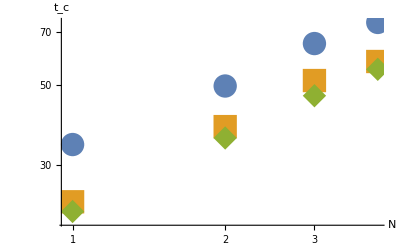

1.37659 x^(2/3)

```mathematica
allTCs = {};
allMeanTCs = {};
allMeanTCsPerM = {};
maxLens = {};
For[m=2, m < 16, m *= 2,
For[g= 100, g < 500,g+= 100,
For[i=0,i<40,i++,
countsArray = simulateChain[g, getFromRandomChoice, m];Z = countsArray[[2]];
	Clear[x];
tC = Length@First@Split[Z,#1==0&];
allTCs = Append[allTCs, tC];
];
maxLens = Append[maxLens, g];
allMeanTCs = Append[allMeanTCs, Mean[allTCs]];
allTCs = {};
];
data = Transpose[{maxLens,allMeanTCs}];allMeanTCsPerM = Append[allMeanTCsPerM, allMeanTCs];allMeanTCs = {};
maxLens = {};
];

Print[allMeanTCsPerM ];ListLogLogPlot[allMeanTCsPerM, AxesLabel -> {"N", "t_c"}, PlotMarkers->{Automatic,24} ]
```

```mathematica
getZAndRest[maxLen_, types_:2] := Module[{allZ, allRest, i},
allZ = {};
allRest = {};
For[i=0,i<10,i++,countsArray = simulateChain[maxLen, types];Z = countsArray[[2]];
allZ = Append[allZ, Z];
allRest = Append[allRest, countsArray[[1]]];
];
meanZ = Mean[allZ];
meanRest = Mean[allRest];
{meanZ, meanRest} ]
```

```mathematica
{meanZ100, meanRest100} = getZAndRest[100];
{meanZ200, meanRest200} = getZAndRest[200];
{meanZ400, meanRest400} = getZAndRest[400];
{meanZ800, meanRest800} = getZAndRest[800];
```

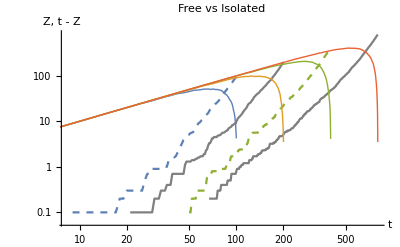

```mathematica
Show[ListLogLogPlot[{meanZ100, meanZ200, meanZ400, meanZ800}, PlotStyle->{Dashed, Gray}, Joined->True], ListLogLogPlot[{meanRest100, meanRest200, meanRest400, meanRest800}, PlotStyle->Thick, Joined->True] , AxesLabel->{HoldForm[t],HoldForm["Z, t - Z"]},PlotLabel->HoldForm[Free vs Isolated]]
```

### Bring me more dimensions! Or at least two for now! ;)

```mathematica
createNeighboursLattice[node_] := {{node[[1]] - 1, node[[2]]}, {node[[1]] + 1, node[[2]]}, {node[[1]], node[[2]] - 1}, {node[[1]], node[[2]] + 1}}
inBoundariesLattice[node_, howLong_] := node[[1]] ≥ 1 && node[[2]] ≥ 1 && node[[1]] ≤ howLong && node[[2]] ≤ howLong
findIsolatedClustersOnLattice[chain_, startNode_, chainSize_] := {isolatedClusterCount = 0; isolatedCount = 0;
howLong = Length[chain];
startNodes =Join[{startNode}, Select[createNeighboursLattice[startNode], inBoundariesLattice[#, chainSize] &]]; 
visited={};
 toVisit = {};centers = {};
While[Length[startNodes] > 0 ,firstNode = Extract[startNodes,1]; startNodes = startNodes[[2;;]];
toVisit = Append[toVisit, firstNode];
currentType = Extract[chain, firstNode];
currentCount = 0; (* used to count how many members are in cluster if it's a cluster *)
fine = False;
While[Length[toVisit] > 0, node = Extract[toVisit, 1]; toVisit = toVisit[[2;;]];
nodeType = Extract[chain,  node];
If[nodeType == 0,fine = True;, If[nodeType == currentType,
currentCount ++;visited = Append[visited, node]; startNodes = DeleteCases[startNodes, node];
neighbours = createNeighboursLattice[node];
toVisit = Join[toVisit, Select[neighbours, inBoundariesLattice[#, howLong] && !MemberQ[visited, #] &]];
If[Length[Select[neighbours, !inBoundariesLattice[#, howLong]&]] > 0, fine=True];
];];
];If[!fine, (* we found an isolated cluster *) isolatedClusterCount++; centers = Append[centers, firstNode]; isolatedCount = isolatedCount + currentCount;]];
{isolatedClusterCount, centers, isolatedCount}}
```

```mathematica
chain = {{1, 1, 1}, {1, -1, 1}, {1, 1, 1}}
```

{{1,1,1},{1,-1,1},{1,1,1}}

```mathematica
findIsolatedClustersOnLattice[chain, {2, 2}, 3]
```

{{1,{{2,2}},1}}

```mathematica
lattice = {{1, 1, 1, 1, 1}, {1, 1, 0, -1, 1}, {1, -1, 1, 1, 1}, {1, 1, -1, 1, 1}, {1, 1, 1, 1, 1}}
```

{{1,1,1,1,1},{1,1,0,-1,1},{1,-1,1,1,1},{1,1,-1,1,1},{1,1,1,1,1}}

```mathematica
lattice // TableForm
```

1 | 1 | 1 | 1 | 1
1 | 1 | 0 | -1 | 1
1 | -1 | 1 | 1 | 1
1 | 1 | -1 | 1 | 1
1 | 1 | 1 | 1 | 1

```mathematica
findIsolatedClustersOnLattice[lattice, {3,3}, 4]
```

{{2,{{4,3},{3,2}},2}}

```mathematica
makeLattice[n_] := Table[Table[0, {i, n}], {j, n}]
makeEmptyIndexesLattice[maxLen_] := Tuples[Table[i, {i, 1, maxLen}],2]
simulateLattice[maxLength_, typeGenerator_: getFromRandomChoice, arg_:2] := Module[{maxLen = maxLength, isolatedCountArray, notIsolatedCountArray, emptyIndexes, chain, iter}, iter = 0;
allIsolated = 0;
isolatedCountArray = {};
notIsolatedCountArray = {};
emptyIndexes = makeEmptyIndexesLattice[maxLen];
chain = makeLattice[maxLen];
While[Length[emptyIndexes] > 0, 
iter++;
(* fill the random empty place with random type *)
x = RandomChoice[emptyIndexes]; emptyIndexes = DeleteCases[emptyIndexes, x]; 
newVal = typeGenerator[arg];
chain[[x[[1]], x[[2]]]] =newVal; 
clusters = findIsolatedClustersOnLattice[chain, x, maxLength];
isolated = clusters[[1, 3]];
allIsolated += isolated;
isolatedCountArray = Append[isolatedCountArray, allIsolated];
notIsolatedCountArray = Append[notIsolatedCountArray, iter - allIsolated];];
{notIsolatedCountArray, isolatedCountArray}]
```

```mathematica
simulateLattice[5]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,23},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2}}

```mathematica
Timing[maxLen = 20;
countsArrayAll ={};
countsArray = simulateLattice[maxLen];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
```

{2.51164,Null}

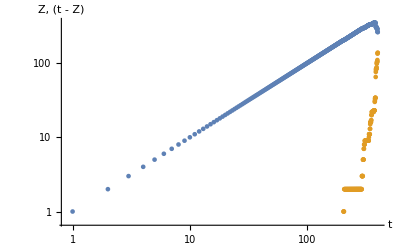

```mathematica
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

### Introducing bias

```mathematica
typeWithBias[bias_]:= RandomVariate[EmpiricalDistribution[{1 /2 + bias,1/ 2 - bias}->{1,2}]]
```

```mathematica
simulateChainWithBias[maxLength_, bias_] := 
simulateChain[maxLen, typeWithBias, bias]
```

```mathematica
maxLen = 2000;
biases = Table[simulateChainWithBias[maxLen,i / 20.0][[2]], {i, 9}];
```

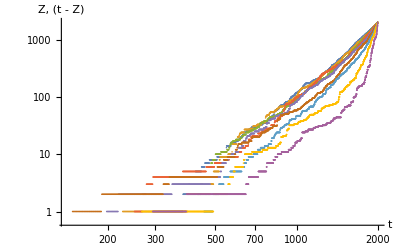

```mathematica
ListLogLogPlot[biases, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
simulateLatticeWithBias[maxLength_, bias_] := 
simulateLattice[maxLength, typeWithBias, bias]
```

```mathematica
maxLen = 20;
biases = Table[simulateLatticeWithBias[maxLen,i / 20.0][[2]], {i, 0,5}];
```

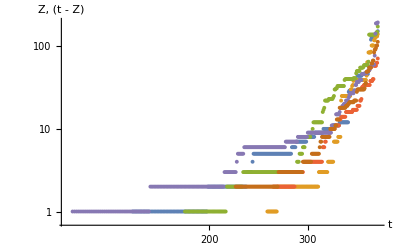

```mathematica
ListLogLogPlot[biases, AxesLabel->{"t", "Z, (t - Z)"}]
```

{1.15238,Null}

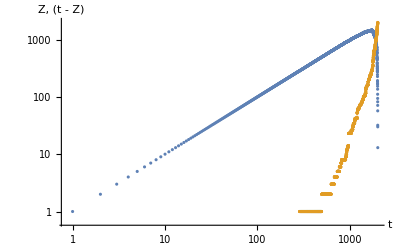

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.4];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

{1.45495,Null}

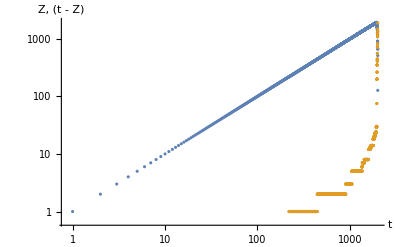

```mathematica
Timing[maxLen = 2000;
countsArrayAll ={};
countsArray = simulateChainWithBias[maxLen, 0.49];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
simulateLatticeWithBias[maxLength_, bias_] := 
simulateLattice[maxLength, typeWithBias, bias]
```

{0.64367,Null}

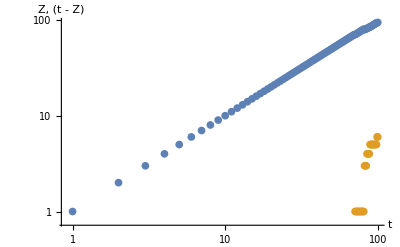

```mathematica
Timing[maxLen = 10;
countsArrayAll ={};
countsArray = simulateLatticeWithBias[maxLen, 0.2];
countsArrayAll = Append[countsArrayAll, countsArray];
countsArray =Mean[countsArrayAll];]
ListLogLogPlot[countsArray, AxesLabel->{"t", "Z, (t - Z)"}]
```

```mathematica
testMe[myFun_, arg_] :=myFun[arg]
```

```mathematica
testMe[Print, 2]
```

2

### Simplifications

```mathematica
If[inBoundariesLattice[neighbour3, howLong], If[!MemberQ[visited, neighbour3], 
toVisit = Append[toVisit, neighbour3];], fine=True];
```

```mathematica
neighbours = {{2, 1}, {2, 3},{1,2},{3, 7}}
```

{{2,1},{2,3},{1,2},{3,7}}

```mathematica
howLong = 4
```

4

```mathematica
visited = {{2, 1}}
```

{{2,1}}

```mathematica
toVisit = {}
```

{}

```mathematica
toVisit = Join[toVisit, Select[neighbours, inBoundariesLattice[#, howLong] && !MemberQ[visited, #] &]]
```

{{2,3},{1,2}}

```mathematica
fine = False
```

False

```mathematica
outOfBoundaries =Select[neighbours, !inBoundariesLattice[#, howLong]&]
```

{{3,7}}

```mathematica
If[Length[Select[neighbours, !inBoundariesLattice[#, howLong]&]] > 0, fine=True];
```

```mathematica
fine
```

True